# Задача 3. Композитные сферические наночастицы ядро в оболочке

Наночастицы полидисперсного нанопорошка алюминия (плотность – 2,7 г/см 3 ) в результате пассивации на воздухе покрыты оболочкой из гамма-оксида алюминия (плотность – 3,6 г/см3) толщиной 3 нм. Порошок характеризуется нормально логарифмическим распределением частиц по размерам при среднемассовом размере 50 нм

Определить массовую долю оксида в пассивированном нанопорошке алюминия.

Исходные данные:

```mathematica
ρ1=Quantity[2.7, ("Grams")/("Centimeters")^3];
ρ2=Quantity[3.6, ("Grams")/("Centimeters")^3];
a=Quantity[3, "Nanometers"];
dw=Quantity[50, "Nanometers"];
```

Схема строения частицы:

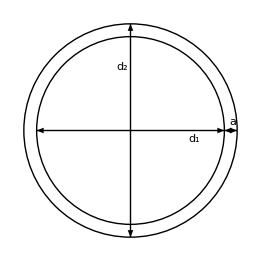

```mathematica
Graphics[{Circle[{0,0},25],Circle[{0,0},(25-3)],
Arrowheads[{-.05,.05}],Arrow[{{-25+3,0},{25-3,0}}],
Arrowheads[{-.05,.05}],Arrow[{{0,-25},{0,25}}],
Arrowheads[{-.03,.03}],Arrow[{{25-3,0},{25,0}}],
Text["d_1",{15,-2}],
Text["d_2",{-2,15}],
Text["a",{24,2}]
}]
```

Из рисунка соотношение диаметров оболочек имеет вид:

d_1=d_2-2a

```mathematica
d1=d2-2a
```

d2+-6 nm

Масса ядра выражается через объем шара и плотность:

```mathematica
m1=(π*d1^3)/6 ρ1; (*Масса ядра*)
m2=((π d2^3)/6-(π d1^3)/6)ρ2;(*Масса оболочки*)
```

Теперь разберемся с среднемассовым размером. Среднемассовый диаметр d_w соотвествует диаметру частицы в такой монодисперсной системе, в которой суммарная масса частиц такая же, как и в данной полидисперсионной системе.

То есть если мы возьмем монодисперсную систему (все частицы одинакового диаметра), то её масса будет такой же как и в нашем случае.

```mathematica
n(m1+m2)/.d2->dw
```

n (1.95477×10^-16 g)

Возможно дейстительно надо делать так:

```mathematica
m2/(m1+m2)/.d2->dw
```

0.383939

Другая идея: рассматриваем распределение.

Логнормальное распределение частиц по диаметрам:

```mathematica
PDF[LogNormalDistribution[Log[μ],Log[σ]],d][[1,1,1]]//TraditionalForm
```

((1.19087 /nm) ⅇ^(-(log(0.335 nm)-log(μ))^2/(2 log^2(σ))))/(log(σ))

Нам неизвестны параметры μ и σ. Они связаны с среднемассовым диаметром, однако найти из из него мы не можем. Так же мы знаем, что у всех частиц размер ядра будет отличаться от размера частицы на константу. То есть σ будет постоянной, отличаются только μ причем на константу.

Тогда распределение ядер будет иметь вид:

```mathematica
PDF[LogNormalDistribution[Log[μ-a],Log[σ]]][1,1,1]
```

(ⅇ^(-Log[μ+-3 nm]^2/(2 Log[σ]^2)))/(√(2 π) Log[σ])

Масса всех частиц тогда будет иметь вид:

```mathematica
m1+m2
```

(d2+-6 nm)^3 (1.41372 g/cm^3)+((d2^3 π)/6-1/6 π (d2+-6 nm)^3) (3.6 g/cm^3)

```mathematica
Mall=∫_0^∞ ((m1+m2)*n/.d2->PDF[LogNormalDistribution[Log[μ],Log[σ]],d][[1,1,1]])ⅆd
```

Integrate::quantd: Missing or incompatible quantities encountered in integration limits {0.335,0,∞}.

∫_0^∞ n ((-6 nm+(ⅇ^(-(-Log[μ]+Log[0.335 nm])^2/(2 Log[σ]^2)) (1.19087 /nm))/Log[σ])^3 (1.41372 g/cm^3)+((ⅇ^(-(3 (-Log[μ]+Log[0.335 nm])^2)/(2 Log[σ]^2)) (0.884289 /nm^3))/Log[σ]^3-1/6 π (-6 nm+(ⅇ^(-(-Log[μ]+Log[0.335 nm])^2/(2 Log[σ]^2)) (1.19087 /nm))/Log[σ])^3) (3.6 g/cm^3))ⅆ(0.335 nm)

```mathematica
Mshell=∫_0^∞ (m2*n/.d2->PDF[LogNormalDistribution[Log[μ-a],Log[σ]]][1,1,1]) ⅆd
```

Integrate::quantd: Missing or incompatible quantities encountered in integration limits {0.335,0,∞}.

∫_0^∞ n ((ⅇ^(-(3 Log[μ+-3 nm]^2)/(2 Log[σ]^2)))/(12 √(2 π) Log[σ]^3)-1/6 π ((ⅇ^(-Log[μ+-3 nm]^2/(2 Log[σ]^2)))/(√(2 π) Log[σ])+-6 nm)^3) (3.6 g/cm^3)ⅆ(0.335 nm)

Искомое соотношение тогда будет отношение этих интегралов:

```mathematica
Mshell/Mall//Simplify
```

(∫_0^∞ n ((ⅇ^(-Log[μ+-3 nm]^2/(2 Log[σ]^2)) (-8.12148×10^-20 g/nm))/Log[σ]+(ⅇ^(-Log[μ+-3 nm]^2/Log[σ]^2) (5.4×10^-21 g/nm^2))/Log[σ]^2+4.0715×10^-19 g)ⅆ(0.335 nm))/(∫_0^∞ 1/Log[σ]^3 n ((Log[σ] (-6 nm)+ⅇ^(-(Log[μ]-Log[0.335 nm])^2/(2 Log[σ]^2)) (1.19087 /nm))^3 (1.41372 g/cm^3)+(0.6 g/cm^3) (-π (Log[σ] (-6 nm)+ⅇ^(-(Log[μ]-Log[0.335 nm])^2/(2 Log[σ]^2)) (1.19087 /nm))^3+ⅇ^(-(3 (Log[μ]-Log[0.335 nm])^2)/(2 Log[σ]^2)) (5.30574 /nm^3)))ⅆ(0.335 nm))